```mathematica
The ASPD models Including PF-670462 
Daewook Kim Jaekyoung Kim
```

```mathematica
The ASPD models were dveloped by perturbing the parameter of which allows for advnacing the phase by ~4 h from the WT model and advacing the phase of gating function g by 4 h to reflect the advanced circadian phase of ASPD patients (Jones et al, Nature Med, 1999). Detailed description of the models can be found in  Materials and Methods and Table EV5.
```

```mathematica
Setting of dosing regimen to simulate PF-670-induced phase shift
```

```mathematica
(* Selection of mutation, which induces advanced sleep phase disorder (ASPD) 
1 -> Per2^t, 2 -> Per2^p, 3 -> Per2^n, 4 -> Gsk3β^a, 5 -> Cry2^t, 6 -> Cry1^t, 7 -> Cry1^d and 8 -> B:C^p*)
select=1;

(*Dosing Days*)
days=21;

(*Light Duration (h)*)
ldd=12;

(*dose level (mpk)*)
dose=26;

(*Dosing Time (h)*)
dtt=4;
```

#### Guideline to simulate the PF-670-induced phase delays in Fig 4B Fig 4B ASPD models: Blue circles 1. Set select=1~8, days=21, ldd=12, dose=26 and dtt=4 2. Set select=1~8, days=21, ldd=12, dose=24 and dtt=5 3. Set select=1~8, days=21, ldd=12, dose=22 and dtt=6 4. Set select=1~8, days=21, ldd=12, dose=19 and dtt=7 Red circles 1. Set select=1~8, days=21, ldd=12, dose=26 and dtt=0 2. Set select=1~8, days=21, ldd=12, dose=24 and dtt=1 3. Set select=1~8, days=21, ldd=12, dose=22 and dtt=2 4. Set select=1~8, days=21, ldd=12, dose=19 and dtt=3

```mathematica
Initial Conditions
```

```mathematica
(*The parameter set of gating and adaptation with the model was referred to as the WT model. Note that this parameter set is the frist set which has the narrow high photosensitivity zone. The description of each parameter can be found in Table EV4.*)
X1=19;
X2=5;
Y1=0.0254792447298582;
Y2=0.09292858771934351;
Z1=6.4674467886106815;
Z2=1.8304664447143064;

(*mutation selection*)
mutants={0.39,2.02,3.05,2.95,5.2,0,3,4.3};
parachange=Table[Table[If[i==j,mutants[[j]],1],{i,1,8}],{j,1,8}];
parachange=parachange[[select]];

(*Initial Condition for the multi-state variable x[j][k][l][m][n]*)
Init1={{{{{{0.},{0.3420612363991834}},{{0.},{8.179771245758342}}},{{{50.57941320972072},{0.}},{{3.084858510765489},{0.}}},{{{0.0985802410460628},{0.}},{{1.3084555441370038},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{41.165766704888945},{0.}},{{0.015608382491794207},{8.720885301950966}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{46.57213430901654},{0.}},{{0.0031953005375601647},{1.36799289498887}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.42289800101916825},{0.}},{{0.},{0.}}},{{{1.0925402835728917},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.0018172208474570813},{0.}},{{0.000051969832456607834},{0.005122234469530184}}},{{{0.1065745913827944},{0.}},{{0.0008330734700784042},{0.0566635532527744}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.0032917376286310976},{0.}},{{0.000014996030154730353},{0.005431344430745013}}},{{{0.08769094840691996},{0.}},{{0.0003337441556398164},{0.05489271181066792}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.0034854600146215606},{0.}},{{0.00001543121168014226},{0.005104574272816484}}},{{{0.09387578379334667},{0.}},{{0.0003536110985068703},{0.053591842109765024}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.9143646209767509},{0.}},{{0.},{0.}}},{{{0.6640388319296585},{0.}},{{0.},{0.}}},{{{0.02261620526647949},{0.}},{{0.},{0.}}},{{{0.024153127001179508},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.003566426542717158},{0.}},{{0.000019446948491991687},{0.0009593633157572193}}},{{{0.25844220368442533},{0.}},{{0.0009853861095753967},{0.024999109498991166}}},{{{0.0001571030498997009},{0.}},{{0.000011241988156917215},{0.0013233693432189286}}},{{{0.010591367829307969},{0.}},{{0.00023061993448538233},{0.025310956921162836}}}},{{{{0.003906943572357614},{0.}},{{0.000013488201348952268},{0.0008093091845965769}}},{{{0.124712274740282},{0.}},{{0.0004168131259404268},{0.014891880773138683}}},{{{0.00018883274230441384},{0.}},{{1.7997916251845195*^-6},{0.0010929293853399464}}},{{{0.005847694864620672},{0.}},{{0.00004358370050515716},{0.01661068549366629}}}},{{{{0.0042845356189285195},{0.}},{{0.000014771592378319274},{0.0008613198533091311}}},{{{0.1376958595595994},{0.}},{{0.00045981124781785865},{0.01603487525209985}}},{{{0.00020679957949088886},{0.}},{{1.9401844427852306*^-6},{0.0011515995567390796}}},{{{0.006446263165149906},{0.}},{{0.00004763488605319544},{0.01770213916985296}}}}},{{{{{0.005698064997206092},{0.}},{{0.00019083191864807688},{0.05668344375489035}}},{{{0.028756909151433502},{0.}},{{0.00041383171976532257},{0.04946506549670688}}},{{{0.0041450474340475356},{0.}},{{0.0003862225731469661},{0.12446417224048362}}},{{{0.0074079613548572055},{0.}},{{0.0006543776273979713},{0.10408853180005757}}}},{{{{0.006669740144184649},{0.}},{{0.00002542209112423298},{0.004845243944628116}}},{{{0.0828541248216783},{0.}},{{0.0002945640707027717},{0.032357261166932494}}},{{{0.0012141988050762562},{0.}},{{0.000011508013921347713},{0.009768583317773775}}},{{{0.008747399124363007},{0.}},{{0.00007984935519557792},{0.06078778560702874}}}},{{{{0.007063852050803612},{0.}},{{0.00002642920327460206},{0.004422509243751679}}},{{{0.08527034138444498},{0.}},{{0.00030090634602644245},{0.030114250838098423}}},{{{0.0013264050530040427},{0.}},{{0.000011249707819832738},{0.00878990944810083}}},{{{0.009150500594118106},{0.}},{{0.00007786053056329725},{0.05558596503417361}}}}},{{{{{0.0007928248680611883},{0.}},{{0.000025780353419672163},{0.0033458239867342923}}},{{{0.0274124885839697},{0.}},{{0.00038549841376936617},{0.05899370416043617}}},{{{0.0001255123171657433},{0.}},{{0.00004997690057380442},{0.007351856000655174}}},{{{0.005502328645107724},{0.}},{{0.0006319867772882921},{0.12768021452441894}}}},{{{{0.0025210125949368953},{0.}},{{0.000010077905400078566},{0.0024810297377193245}}},{{{0.05812325888303372},{0.}},{{0.00020742923534716493},{0.023913749818730998}}},{{{0.00030530718232012633},{0.}},{{4.902173374599667*^-6},{0.005219487814016039}}},{{{0.007539434826295608},{0.}},{{0.00006395851528373895},{0.04714353907964912}}}},{{{{0.0025977211835363366},{0.}},{{0.00001017089395981654},{0.002248072566075126}}},{{{0.060247906870995155},{0.}},{{0.00021344857807776635},{0.022578312737100606}}},{{{0.0003200670130454894},{0.}},{{4.603722758559816*^-6},{0.004701002286841585}}},{{{0.007971833585551605},{0.}},{{0.00006352606272272561},{0.04407940585392828}}}}}};

(*Initial Condition for the single-state variable*)
Init2={0.21004770358705036,0.7879547112081645,1.1383721663365372,3.760854376307055,1.095465622771389,12.37354665811613,4.470535676137161,4.189465465043962,0.5791077386453771,8.349625799238817,1.4116789475658296,35.184199298572295,8.56043138049844,23.77410578150899,0.5893077833141493,0.40424721668584945,48.09767559849965,31.869023309234613,161.14372712932516,123.95046120625604,467.84444843738225,0.1932885142503498,58.23913168018502,0.03971373557862615,19.06619007243528,0.5999649539384736,0.39359004606153003,0,0.11012045498612394,67.61745646537098,0,0,6.5815025579914295,0.4162165798701546,0.5585648324701572,0.25595982171319526,0.5203673130406197,0.19388642676798773,0.8044041532454284};
```

```mathematica
Parameter 
Detailed description can be found in Table EV3 and 4
```

```mathematica
(*Transcription Rate*)
trPo=25.9201;trPt=parachange[[1]]*44.854;trRo=parachange[[6]]*23.0747;trRt=parachange[[5]]*39.9409;trB=46.1038;trRev=102.92299999999999;trNp=0.3297485941817571;

(*Translation Rate*)
tlp=1.81031;tlr=5.03882;tlb=0.530436;tlrev=8.90744;tlc=4.645890;tlnp=1.25099;

(*Binding/Unbinding Rate between Proteins*)
agp=1.3962;dg=2.93521;ac=0.0456572;dc=0.108072;ar=0.0235285;dr=0.605268;cbin=0.0454894;uncbin=7.27215;
bbin=6.92686;unbbin=0.130196;cbbin=6.59924;uncbbin=0.304176;ag=0.162392;

(*Binding/Unbinding Rate on Promoters*)
bin=6.97166;unbin=0.255032;binrev=0.0120525;unbinrev=10.9741;binr=6.15445;unbinr=2.91009;binc=0.280863;
unbinc=0.00886752;binrevb=0.00626588;unbinrevb=5.30559;

(*Translocation Rate*)
tmc=0.16426;tmcrev=9.2631;nl=0.643086;ne=0.0269078;nlrev=9.63702;nerev=0.0152514;lne=0.594609;nlbc=5.26501;

(*Phosphorylation Rate*)
hoo=0.527453;hto=parachange[[2]]*2.45584;phos=parachange[[8]]*0.291429;

(*Light Effet*)
lono=2.430974274075263;
lont=4.6820111190704266;

(*GSK3b Activity*)
trgto=0.644602;ugto=parachange[[4]]*0.0625777;

(*Ratio beteeen Cytoplasm and Nucleus*)
Nf=3.35063;

(*Degradation Rate*)
up=3.537;uro=parachange[[7]]*0.17491;urt=0.481895;umNp=0.369493;
umPo=0.76696222;umPt=0.58891980;umRo=0.40342526000000006;umRt=0.45554418;ub=0.018800209999999998;uc=0.025165115999999998;
ubc=0.34882936000000003;upu=0.0700322;urev=1.6487614725107194;uprev=0.5173026723236928;umB=0.7954019999999999;umRev=1.510194;

(*Initial free plasma concentration of CK1 inhibitor (10mpk)*)
prodi=6562.5;
(*Transfer rate from plasma to brain for CK1 inhibitor*)
nlpin=1;
(*Transfer rate from brain to plasma for CK1 inhibitor*)
nepin=1;
(*Transfer rate from brain to cell for CK1 inhibitor*)
nlbin=0.15;
(*Transfer rate from cell to brain for CK1 inhibitor*)
nebin=23;
(*Nuclear localization rate constant for CKI inhibitor*)
nlin=0.533183;
(*Nuclear export rate constant for CKI inhibitor*)
nein=0.192038;
(*Nuclear export rate constant for CKI and CKI inhibitor complex*)
lnei=0.0472142;
(*Binding rate constant for CKI inhibitor to CKI*)
inbin=0.42118;
(*Unbinding rate constant for CKI inhibitor to CKI*)
inubin=3.38008;
(*Clearance rate constant for free CKI inhibitor in blood plasma*)
uinp=2;
```

```mathematica
Equations for Single-state Variables while light is off
Detailed description can be found in Appendix Equation 1 and Table EV1
```

```mathematica
daone={
(*Original model equations*)
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t])-unbinc*Gc[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*G[t]-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*G[t]-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*Gc[t]-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*Gr[t]-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*G[t]*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t],

(*Free Blood Plsma Concentration*)
pInh'[t]==-(uinp+nlpin)*pInh[t]+nepin*bInh[t],

(*Free Brain Tissue Concentration*)
bInh'[t]==-(nlbin+nepin)*bInh[t]+nlpin*pInh[t]+nebin*Inh[t],

(*Free Cytoplasm Concentration*)
Inh'[t]==nlbin*bInh[t]-(nebin+nlin)*Inh[t]+nein*nInh[t]+(-inbin*Inh[t]*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,1,3,2}])+inubin*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,4,5}],

(*Free Nucleus Concentration*)
nInh'[t]==Inh[t]*nlin-(nein)*nInh[t]-(inbin*Nf*nInh[t]*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,1,3,2},{nn,0,1}])+inubin*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,4,5},{nn,0,1}]

};
```

```mathematica
Equations for Multi-state Variables (Protein complexes)
Detailed description can be found in Appendix Equation 1 and Table EV2
```

```mathematica
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==
(*CK1-CK1 Inhibitor Binidng/Unbinidng*)
If[(l==1)&&(m==0)&&(n==0),-inbin*Inh[t]*x[j][k][l][m][n][t]+inubin*x[j][k][4][m][n][t],0]+If[(l==3)&&(m==0)&&(n==0),-inbin*Inh[t]*x[j][k][l][m][n][t]+inubin*x[j][k][5][m][n][t],0]+If[(l==4)&&(m==0)&&(n==0),inbin*Inh[t]*x[j][k][1][m][n][t]-inubin*x[j][k][l][m][n][t],0]+If[(l==5)&&(m==0)&&(n==0),inbin*Inh[t]*x[j][k][3][m][n][t]-inubin*x[j][k][l][m][n][t],0]+If[(l==1)&&(m==1),-inbin*Nf*nInh[t]*x[j][k][l][m][n][t]+inubin*x[j][k][4][m][n][t],0]+If[(l==3)&&(m==1),-inbin*Nf*nInh[t]*x[j][k][l][m][n][t]+inubin*x[j][k][5][m][n][t],0]+
If[(l==4)&&(m==1),inbin*Nf*nInh[t]*x[j][k][1][m][n][t]-inubin*x[j][k][l][m][n][t],0]+
If[(l==5)&&(m==1),inbin*Nf*nInh[t]*x[j][k][3][m][n][t]-inubin*x[j][k][l][m][n][t],0]+

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,5}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,5}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,5}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,5}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,5}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,5}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[0][0][ll][m][0][t],{ll,1,4,3}]+dc*Sum[x[j][k][ll][m][n][t],{ll,1,4,3}],0]+If[(j==0)&&(k==0)&&((l==1)||(l==4))&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+If[(j>0)&&((l==1)||(l==4))&&(n==0),ac*If[m==1,Nf,1]*x[0][0][l][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[0][0][ll][m][0][t],{ll,1,4,3}]+dc*Sum[x[j][k][ll][m][n][t],{ll,1,4,3}],0]+If[(j==0)&&(k==0)&&((l==1)||(l==4))&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&((l==1)||(l==4))&&(m==1)&&(n==1),ac*Nf*x[0][0][l][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+
If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[j][k][2][m][n][t]*x[0][0][1][m][0][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][4][m][0][t]+dc*x[j][k][5][m][n][t],0]+If[(j==0)&&(k==0)&&(l==4)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][5][m][0][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==5)&&(n==0),ac*If[m==1,Nf,1]*x[j][k][2][m][n][t]*x[0][0][4][m][0][t]-dc*x[j][k][l][m][n][t],0]+If[(l==2)&&(j>2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==2)&&(j>2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][4][m][0][t]+dc*x[j][k][5][m][n][t],0]+If[(j==0)&&(k==0)&&(l==4)&&(m==1)&&(n==0),-ac*Nf*x[j][j][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][5][m][1][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==5)&&(m==1)&&(n==1),ac*Nf*x[0][0][4][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j>2)&&(l==4),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][5][m][n][t],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==5),If[m==1,Nf,1]*agp*x[j][k][4][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,{0,1,4}},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,{2,3,5}},{nn,0,1}],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(n>0)&&(l==0)&&(m==1),-bbin*Nf*x[0][0][0][m][n][t]*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,5}]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,5}],0]+If[(j>0)&&(m==1)&&(n>0),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+

(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*If[(j==4)||(j==5)||(j==6),parachange[[3]],1]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*If[(j==4)||(j==5)||(j==6),parachange[[3]],1]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*CK1-CK1 inhibitor Complex Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==4))&&(m==1)&&(n==0),-lnei*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==4))&&(m==0)&&(n==0),lnei*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)||(l==5)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)||(l==5)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,4,6,2},{nn,0,1},{ll,1,3,2}]+up*Sum[x[jj][0][ll][m][nn][t],{jj,2,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+If[(j==0)&&(k==0)&&(l==4)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,4,6,2},{nn,0,1},{ll,4,5}]+up*Sum[x[jj][0][ll][m][nn][t],{jj,2,2},{nn,0,1},{ll,4,5}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,4,5}],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,4,6,2},{ll,{2,3,5}},{nn,0,1}]+
up*Sum[x[jj][0][ll][m][nn][t],{jj,2,2},{ll,{2,3,5}},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,{2,3,5}},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,4,6,2},{ll,0,5}]+up*Sum[x[jj][0][ll][m][n][t],{jj,2,2},{ll,0,5}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,5}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
```

```mathematica
Incorporation of gating and adaptation for light into the model
```

```mathematica
(*Contruction of adaptation function*)
adap[x_]:=-(x^Z2/(x^Z2+Z1^Z2))+1;

(*Contruction of gating, function g, which describes the photosensitivity of circadian clock  at each circadian time*)
connectlowtohigh=NonlinearModelFit[{{24-X2,Y1},{24,Y1},{24-0.5*X2,Y2}},q0+q1*x+q2*x^2+q3*x^3+q4*x^4,{q0,q1,q2,q3,q4},x];
interpol=Join[Table[Y1,{x,0,24-X2,0.01}],Table[connectlowtohigh[x],{x,24-X2+0.01,24,0.01}]];
interpol=RotateRight[interpol,(X1+X2-24)*100];
(*Reflecting the advanced circadian phase of ASPD patients, the phase of gating function g is advancd by 4 h*)
interpol=RotateRight[interpol,-400];
g=Interpolation[Table[{i*0.01,interpol[[i+1]]},{i,0,2400}]];
```

```mathematica
(*Construction of function p which determines the CT from an internal pace marker: the phase angle of the limit cycle of the two clock variables*)

(*Step1: LD 12:12 entraiment*)
```

```mathematica
Equations for Single-state Variables while light is on 
Detailed description can be found in  Appendix Equation1 and Table EV1
laone1: This equation is used for entraining the model to LD 12:12 to correspond CTx to ZTx, which is the step1 to construct the function p
Thus ,light module is modelled just as g[t]*adap[t] (not g[p[revng[t],revnp[t]]]*adap[t]) (note that while t is between 0 and 12, the light is on).
```

```mathematica
laone1={
(*Original model equations*)
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t])-unbinc*Gc[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*G[t]-tmc*MnPo[t]-umPo*MnPo[t]+lono*trPo*g[t]*adap[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*G[t]-tmc*MnPt[t]-umPt*MnPt[t]+lont*trPt*g[t]*adap[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*Gc[t]-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*Gr[t]-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*G[t]*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t],

(*Free Blood Plsma Concentration*)
pInh'[t]==-(uinp+nlpin)*pInh[t]+nepin*bInh[t],

(*Free Brain Tissue Concentration*)
bInh'[t]==-(nlbin+nepin)*bInh[t]+nlpin*pInh[t]+nebin*Inh[t],

(*Free Cytoplasm Concentration*)
Inh'[t]==nlbin*bInh[t]-(nebin+nlin)*Inh[t]+nein*nInh[t]+(-inbin*Inh[t]*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,1,3,2}])+inubin*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,4,5}],
(*Free Nucleus Concentration*)
nInh'[t]==Inh[t]*nlin-(nein)*nInh[t]-(inbin*Nf*nInh[t]*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,1,3,2},{nn,0,1}])+inubin*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,4,5},{nn,0,1}]

};
```

```mathematica
ldt=12;

phase={};

iternum=2;

For[jjj=1,jjj<3,jjj++,

If[jjj==1,
athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[36]],MnNp[0]==Init2[[37]],Gc[0]==Init2[[38]],GcR[0]==Init2[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};
afour=Flatten[Table[x[j][k][l][m][n][0]==If[l>3,0,Init1[[j+1,k+1,l+1,m+1,n+1,1]]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];,
Init11=Table[x[j][k][l][m][n][24-ldt]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];Init22=Flatten[{G[24-ldt]/.qrt22,GR[24-ldt]/.qrt22,gto[24-ldt]/.qrt22,MnRo[24-ldt]/.qrt22,McRo[24-ldt]/.qrt22,MnRt[24-ldt]/.qrt22,McRt[24-ldt]/.qrt22,MnPo[24-ldt]/.qrt22,McPo[24-ldt]/.qrt22,MnPt[24-ldt]/.qrt22,McPt[24-ldt]/.qrt22,MnB[24-ldt]/.qrt22,McB[24-ldt]/.qrt22,B[24-ldt]/.qrt22,GBb[24-ldt]/.qrt22,GBRb[24-ldt]/.qrt22,Cl[24-ldt]/.qrt22,MnRev[24-ldt]/.qrt22,McRev[24-ldt]/.qrt22,cyrev[24-ldt]/.qrt22,revn[24-ldt]/.qrt22,cyrevg[24-ldt]/.qrt22,revng[24-ldt]/.qrt22,cyrevgp[24-ldt]/.qrt22,revngp[24-ldt]/.qrt22,GB[24-ldt]/.qrt22,GBR[24-ldt]/.qrt22,0,cyrevp[24-ldt]/.qrt22,revnp[24-ldt]/.qrt22,0,0,BC[24-ldt]/.qrt22,Gr[24-ldt]/.qrt22,GrR[24-ldt]/.qrt22,McNp[24-ldt]/.qrt22,MnNp[24-ldt]/.qrt22,Gc[24-ldt]/.qrt22,GcR[24-ldt]/.qrt22}];
athree={G[0]==Init22[[1]],GR[0]==Init22[[2]],gto[0]==Init22[[3]],MnRo[0]==Init22[[4]],McRo[0]==Init22[[5]],MnRt[0]==Init22[[6]],McRt[0]==Init22[[7]],MnPo[0]==Init22[[8]],McPo[0]==Init22[[9]],MnPt[0]==Init22[[10]],McPt[0]==Init22[[11]],MnB[0]==Init22[[12]],McB[0]==Init22[[13]],B[0]==Init22[[14]],GBb[0]==Init22[[15]],GBRb[0]==Init22[[16]],Cl[0]==Init22[[17]],MnRev[0]==Init22[[18]],McRev[0]==Init22[[19]],cyrev[0]==Init22[[20]],revn[0]==Init22[[21]],cyrevg[0]==Init22[[22]],revng[0]==Init22[[23]],cyrevgp[0]==Init22[[24]],revngp[0]==Init22[[25]],GB[0]==Init22[[26]],GBR[0]==Init22[[27]],cyrevp[0]==Init22[[29]],revnp[0]==Init22[[30]],BC[0]==Init22[[33]],Gr[0]==Init22[[34]],GrR[0]==Init22[[35]],McNp[0]==Init22[[36]],MnNp[0]==Init22[[37]],Gc[0]==Init22[[38]],GcR[0]==Init22[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};
afour=Flatten[Table[x[j][k][l][m][n][0]==Init11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]]];
afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,pInh,nInh,bInh,Inh,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]]];
qrt2=NDSolve[Join[laone1,atwo,athree,afour],afive,{t,0,ldt},MaxSteps->100000,MaxStepSize->0.1];

Init11=Table[x[j][k][l][m][n][ldt]/.qrt2,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];Init22=Flatten[{G[ldt]/.qrt2,GR[ldt]/.qrt2,gto[ldt]/.qrt2,MnRo[ldt]/.qrt2,McRo[ldt]/.qrt2,MnRt[ldt]/.qrt2,McRt[ldt]/.qrt2,MnPo[ldt]/.qrt2,McPo[ldt]/.qrt2,MnPt[ldt]/.qrt2,McPt[ldt]/.qrt2,MnB[ldt]/.qrt2,McB[ldt]/.qrt2,B[ldt]/.qrt2,GBb[ldt]/.qrt2,GBRb[ldt]/.qrt2,Cl[ldt]/.qrt2,MnRev[ldt]/.qrt2,McRev[ldt]/.qrt2,cyrev[ldt]/.qrt2,revn[ldt]/.qrt2,cyrevg[ldt]/.qrt2,revng[ldt]/.qrt2,cyrevgp[ldt]/.qrt2,revngp[ldt]/.qrt2,GB[ldt]/.qrt2,GBR[ldt]/.qrt2,0,cyrevp[ldt]/.qrt2,revnp[ldt]/.qrt2,0,0,BC[ldt]/.qrt2,Gr[ldt]/.qrt2,GrR[ldt]/.qrt2,McNp[ldt]/.qrt2,MnNp[ldt]/.qrt2,Gc[ldt]/.qrt2,GcR[ldt]/.qrt2}];athree={G[0]==Init22[[1]],GR[0]==Init22[[2]],gto[0]==Init22[[3]],MnRo[0]==Init22[[4]],McRo[0]==Init22[[5]],MnRt[0]==Init22[[6]],McRt[0]==Init22[[7]],MnPo[0]==Init22[[8]],McPo[0]==Init22[[9]],MnPt[0]==Init22[[10]],McPt[0]==Init22[[11]],MnB[0]==Init22[[12]],McB[0]==Init22[[13]],B[0]==Init22[[14]],GBb[0]==Init22[[15]],GBRb[0]==Init22[[16]],Cl[0]==Init22[[17]],MnRev[0]==Init22[[18]],McRev[0]==Init22[[19]],cyrev[0]==Init22[[20]],revn[0]==Init22[[21]],cyrevg[0]==Init22[[22]],revng[0]==Init22[[23]],cyrevgp[0]==Init22[[24]],revngp[0]==Init22[[25]],GB[0]==Init22[[26]],GBR[0]==Init22[[27]],cyrevp[0]==Init22[[29]],revnp[0]==Init22[[30]],BC[0]==Init22[[33]],Gr[0]==Init22[[34]],GrR[0]==Init22[[35]],McNp[0]==Init22[[36]],MnNp[0]==Init22[[37]],Gc[0]==Init22[[38]],GcR[0]==Init22[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};afour=Flatten[Table[x[j][k][l][m][n][0]==Init11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt22=NDSolve[Join[daone,atwo,athree,afour],afive,{t,0,24-ldt},MaxSteps->100000,MaxStepSize->0.1];

phase=Join[phase,{Join[Table[MnB[t]/.qrt2[[1]],{t,0,ldt,2}],Table[MnB[t]/.qrt22[[1]],{t,2,24-ldt,2}]]}];

];

imInit11=Table[x[j][k][l][m][n][24-ldt]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];imInit22=Flatten[{G[24-ldt]/.qrt22,GR[24-ldt]/.qrt22,gto[24-ldt]/.qrt22,MnRo[24-ldt]/.qrt22,McRo[24-ldt]/.qrt22,MnRt[24-ldt]/.qrt22,McRt[24-ldt]/.qrt22,MnPo[24-ldt]/.qrt22,McPo[24-ldt]/.qrt22,MnPt[24-ldt]/.qrt22,McPt[24-ldt]/.qrt22,MnB[24-ldt]/.qrt22,McB[24-ldt]/.qrt22,B[24-ldt]/.qrt22,GBb[24-ldt]/.qrt22,GBRb[24-ldt]/.qrt22,Cl[24-ldt]/.qrt22,MnRev[24-ldt]/.qrt22,McRev[24-ldt]/.qrt22,cyrev[24-ldt]/.qrt22,revn[24-ldt]/.qrt22,cyrevg[24-ldt]/.qrt22,revng[24-ldt]/.qrt22,cyrevgp[24-ldt]/.qrt22,revngp[24-ldt]/.qrt22,GB[24-ldt]/.qrt22,GBR[24-ldt]/.qrt22,0,cyrevp[24-ldt]/.qrt22,revnp[24-ldt]/.qrt22,0,0,BC[24-ldt]/.qrt22,Gr[24-ldt]/.qrt22,GrR[24-ldt]/.qrt22,McNp[24-ldt]/.qrt22,MnNp[24-ldt]/.qrt22,Gc[24-ldt]/.qrt22,GcR[24-ldt]/.qrt22}];

While[Sqrt[Total[((phase[[2]]-phase[[1]])/phase[[1]])^2]]>0.005,

iternum++;
phase[[1]]=phase[[2]];

Init1=imInit11;
Init2=imInit22;

athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[36]],MnNp[0]==Init2[[37]],Gc[0]==Init2[[38]],GcR[0]==Init2[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};
afour=Flatten[Table[x[j][k][l][m][n][0]==If[l>3,0,Init1[[j+1,k+1,l+1,m+1,n+1,1]]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,pInh,nInh,bInh,Inh,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]]];
qrt2=NDSolve[Join[laone1,atwo,athree,afour],afive,{t,0,ldt},MaxSteps->100000,MaxStepSize->0.1];

Init11=Table[x[j][k][l][m][n][ldt]/.qrt2,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];Init22=Flatten[{G[ldt]/.qrt2,GR[ldt]/.qrt2,gto[ldt]/.qrt2,MnRo[ldt]/.qrt2,McRo[ldt]/.qrt2,MnRt[ldt]/.qrt2,McRt[ldt]/.qrt2,MnPo[ldt]/.qrt2,McPo[ldt]/.qrt2,MnPt[ldt]/.qrt2,McPt[ldt]/.qrt2,MnB[ldt]/.qrt2,McB[ldt]/.qrt2,B[ldt]/.qrt2,GBb[ldt]/.qrt2,GBRb[ldt]/.qrt2,Cl[ldt]/.qrt2,MnRev[ldt]/.qrt2,McRev[ldt]/.qrt2,cyrev[ldt]/.qrt2,revn[ldt]/.qrt2,cyrevg[ldt]/.qrt2,revng[ldt]/.qrt2,cyrevgp[ldt]/.qrt2,revngp[ldt]/.qrt2,GB[ldt]/.qrt2,GBR[ldt]/.qrt2,0,cyrevp[ldt]/.qrt2,revnp[ldt]/.qrt2,0,0,BC[ldt]/.qrt2,Gr[ldt]/.qrt2,GrR[ldt]/.qrt2,McNp[ldt]/.qrt2,MnNp[ldt]/.qrt2,Gc[ldt]/.qrt2,GcR[ldt]/.qrt2}];athree={G[0]==Init22[[1]],GR[0]==Init22[[2]],gto[0]==Init22[[3]],MnRo[0]==Init22[[4]],McRo[0]==Init22[[5]],MnRt[0]==Init22[[6]],McRt[0]==Init22[[7]],MnPo[0]==Init22[[8]],McPo[0]==Init22[[9]],MnPt[0]==Init22[[10]],McPt[0]==Init22[[11]],MnB[0]==Init22[[12]],McB[0]==Init22[[13]],B[0]==Init22[[14]],GBb[0]==Init22[[15]],GBRb[0]==Init22[[16]],Cl[0]==Init22[[17]],MnRev[0]==Init22[[18]],McRev[0]==Init22[[19]],cyrev[0]==Init22[[20]],revn[0]==Init22[[21]],cyrevg[0]==Init22[[22]],revng[0]==Init22[[23]],cyrevgp[0]==Init22[[24]],revngp[0]==Init22[[25]],GB[0]==Init22[[26]],GBR[0]==Init22[[27]],cyrevp[0]==Init22[[29]],revnp[0]==Init22[[30]],BC[0]==Init22[[33]],Gr[0]==Init22[[34]],GrR[0]==Init22[[35]],McNp[0]==Init22[[36]],MnNp[0]==Init22[[37]],Gc[0]==Init22[[38]],GcR[0]==Init22[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};afour=Flatten[Table[x[j][k][l][m][n][0]==Init11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt22=NDSolve[Join[daone,atwo,athree,afour],afive,{t,0,24-ldt},MaxSteps->100000,MaxStepSize->0.1];

phase[[2]]=Join[Table[MnB[t]/.qrt2[[1]],{t,0,ldt,2}],Table[MnB[t]/.qrt22[[1]],{t,2,24-ldt,2}]];

imInit11=Table[x[j][k][l][m][n][24-ldt]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];imInit22=Flatten[{G[24-ldt]/.qrt22,GR[24-ldt]/.qrt22,gto[24-ldt]/.qrt22,MnRo[24-ldt]/.qrt22,McRo[24-ldt]/.qrt22,MnRt[24-ldt]/.qrt22,McRt[24-ldt]/.qrt22,MnPo[24-ldt]/.qrt22,McPo[24-ldt]/.qrt22,MnPt[24-ldt]/.qrt22,McPt[24-ldt]/.qrt22,MnB[24-ldt]/.qrt22,McB[24-ldt]/.qrt22,B[24-ldt]/.qrt22,GBb[24-ldt]/.qrt22,GBRb[24-ldt]/.qrt22,Cl[24-ldt]/.qrt22,MnRev[24-ldt]/.qrt22,McRev[24-ldt]/.qrt22,cyrev[24-ldt]/.qrt22,revn[24-ldt]/.qrt22,cyrevg[24-ldt]/.qrt22,revng[24-ldt]/.qrt22,cyrevgp[24-ldt]/.qrt22,revngp[24-ldt]/.qrt22,GB[24-ldt]/.qrt22,GBR[24-ldt]/.qrt22,0,cyrevp[24-ldt]/.qrt22,revnp[24-ldt]/.qrt22,0,0,BC[24-ldt]/.qrt22,Gr[24-ldt]/.qrt22,GrR[24-ldt]/.qrt22,McNp[24-ldt]/.qrt22,MnNp[24-ldt]/.qrt22,Gc[24-ldt]/.qrt22,GcR[24-ldt]/.qrt22}];

If[iternum>99,Break[]];

];
```

```mathematica
(*Step2: corresponding each phase angle of limit cycle to a specific ZT(CT)*)
XXo=Table[revng[t]/.qrt2[[1]],{t,0,ldt,0.01}];
XXt=Table[revng[t]/.qrt22[[1]],{t,0.01,24-ldt,0.01}];
YYo=Table[revnp[t]/.qrt2[[1]],{t,0,ldt,0.01}];
YYt=Table[revnp[t]/.qrt22[[1]],{t,0.01,24-ldt,0.01}];
XX=Join[XXo,XXt];
YY=Join[YYo,YYt];

max1=Max[XX];
min1=Min[XX];
max2=Max[YY];
min2=Min[YY];
center1=N[(max1+min1)/2]/max1;
center2=N[(max2+min2)/2]/max2;

polar=ToPolarCoordinates[Table[{XX[[i+1]]/Max[XX]-center1,YY[[i+1]]/Max[YY]-center2},{i,0,2400}]];
angle={};

For[i=1,i<2402,i++,
angle=Join[angle,{polar[[i]][[2]]}];

];
angle=Mod[angle,2*Pi];

p=Interpolation[Sort[Table[{angle[[i]],0.01*i-0.01},{i,1,2401}]]];
```

```mathematica
(*Construction of the Composition of g and p, g▪p*)
circle=Sort[Table[{angle[[i]],g[p[angle[[i]]]]},{i,1,2401}]];

If[2*Pi-Max[angle]<Min[angle],
circle=Join[circle,{{0,circle[[2401]][[2]]},{2*Pi,circle[[2401]][[2]]}}];
,
circle=Join[circle,{{0,circle[[1]][[2]]},{2*Pi,circle[[1]][[2]]}}];
];

(*function1: Construction of g▪p usuing Interpolation function*)
function1=Interpolation[circle];

(*function2: Approximation (Construction) of g▪p using Fourier series*)
k=100;
para1=Table[a[i],{i,0,k}];
para2=Table[b[i],{i,1,k}];

function2=NonlinearModelFit[circle,a[0]+Sum[a[i]*Sin[i*w*x]+b[i]*Cos[i*w*x],{i,1,k}],Join[para1,para2,{w}],x];

compositgp=function2;
```

```mathematica
Simulation of Chronic Dosing under LD cycle
```

```mathematica
Entrainment to LD cycle before dosing
```

```mathematica
Equations for Single-state Variables while light is on 
Detailed description can be found in  Appendix Equation1 and Table EV1
laone2: The function p is incorporated into the light module
```

```mathematica
laone2={
(*Original model equations*)
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t])-unbinc*Gc[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription - gating and adaptation for light are incorporated*)
MnPo'[t]==trPo*G[t]-tmc*MnPo[t]-umPo*MnPo[t]+lono*trPo*compositgp[Mod[ArcTan[revng[t]/max1-center1,revnp[t]/max2-center2],2*Pi]]*adap[t],
McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*G[t]-tmc*MnPt[t]-umPt*MnPt[t]+lont*trPt*compositgp[Mod[ArcTan[revng[t]/max1-center1,revnp[t]/max2-center2],2*Pi]]*adap[t],
McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*Gc[t]-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*Gr[t]-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*G[t]*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t],

(*Free Blood Plsma Concentration*)
pInh'[t]==-(uinp+nlpin)*pInh[t]+nepin*bInh[t],

(*Free Brain Tissue Concentration*)
bInh'[t]==-(nlbin+nepin)*bInh[t]+nlpin*pInh[t]+nebin*Inh[t],

(*Free Cytoplasm Concentration*)
Inh'[t]==nlbin*bInh[t]-(nebin+nlin)*Inh[t]+nein*nInh[t]+(-inbin*Inh[t]*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,1,3,2}])+inubin*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,4,5}],
(*Free Nucleus Concentration*)
nInh'[t]==Inh[t]*nlin-(nein)*nInh[t]-(inbin*Nf*nInh[t]*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,1,3,2},{nn,0,1}])+inubin*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,4,5},{nn,0,1}]

};
```

```mathematica
Init1=imInit11;
Init2=imInit22;

phase={};

iternum=2;

For[jjj=1,jjj<3,jjj++,

If[jjj==1,
athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[36]],MnNp[0]==Init2[[37]],Gc[0]==Init2[[38]],GcR[0]==Init2[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};
afour=Flatten[Table[x[j][k][l][m][n][0]==If[l>3,0,Init1[[j+1,k+1,l+1,m+1,n+1,1]]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];,
Init11=Table[x[j][k][l][m][n][24-ldd]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];Init22=Flatten[{G[24-ldd]/.qrt22,GR[24-ldd]/.qrt22,gto[24-ldd]/.qrt22,MnRo[24-ldd]/.qrt22,McRo[24-ldd]/.qrt22,MnRt[24-ldd]/.qrt22,McRt[24-ldd]/.qrt22,MnPo[24-ldd]/.qrt22,McPo[24-ldd]/.qrt22,MnPt[24-ldd]/.qrt22,McPt[24-ldd]/.qrt22,MnB[24-ldd]/.qrt22,McB[24-ldd]/.qrt22,B[24-ldd]/.qrt22,GBb[24-ldd]/.qrt22,GBRb[24-ldd]/.qrt22,Cl[24-ldd]/.qrt22,MnRev[24-ldd]/.qrt22,McRev[24-ldd]/.qrt22,cyrev[24-ldd]/.qrt22,revn[24-ldd]/.qrt22,cyrevg[24-ldd]/.qrt22,revng[24-ldd]/.qrt22,cyrevgp[24-ldd]/.qrt22,revngp[24-ldd]/.qrt22,GB[24-ldd]/.qrt22,GBR[24-ldd]/.qrt22,0,cyrevp[24-ldd]/.qrt22,revnp[24-ldd]/.qrt22,0,0,BC[24-ldd]/.qrt22,Gr[24-ldd]/.qrt22,GrR[24-ldd]/.qrt22,McNp[24-ldd]/.qrt22,MnNp[24-ldd]/.qrt22,Gc[24-ldd]/.qrt22,GcR[24-ldd]/.qrt22}];
athree={G[0]==Init22[[1]],GR[0]==Init22[[2]],gto[0]==Init22[[3]],MnRo[0]==Init22[[4]],McRo[0]==Init22[[5]],MnRt[0]==Init22[[6]],McRt[0]==Init22[[7]],MnPo[0]==Init22[[8]],McPo[0]==Init22[[9]],MnPt[0]==Init22[[10]],McPt[0]==Init22[[11]],MnB[0]==Init22[[12]],McB[0]==Init22[[13]],B[0]==Init22[[14]],GBb[0]==Init22[[15]],GBRb[0]==Init22[[16]],Cl[0]==Init22[[17]],MnRev[0]==Init22[[18]],McRev[0]==Init22[[19]],cyrev[0]==Init22[[20]],revn[0]==Init22[[21]],cyrevg[0]==Init22[[22]],revng[0]==Init22[[23]],cyrevgp[0]==Init22[[24]],revngp[0]==Init22[[25]],GB[0]==Init22[[26]],GBR[0]==Init22[[27]],cyrevp[0]==Init22[[29]],revnp[0]==Init22[[30]],BC[0]==Init22[[33]],Gr[0]==Init22[[34]],GrR[0]==Init22[[35]],McNp[0]==Init22[[36]],MnNp[0]==Init22[[37]],Gc[0]==Init22[[38]],GcR[0]==Init22[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};
afour=Flatten[Table[x[j][k][l][m][n][0]==Init11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]]];
afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,pInh,nInh,bInh,Inh,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]]];
qrt2=NDSolve[Join[laone2,atwo,athree,afour],afive,{t,0,ldd},MaxSteps->100000,MaxStepSize->0.1];

Init11=Table[x[j][k][l][m][n][ldd]/.qrt2,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];Init22=Flatten[{G[ldd]/.qrt2,GR[ldd]/.qrt2,gto[ldd]/.qrt2,MnRo[ldd]/.qrt2,McRo[ldd]/.qrt2,MnRt[ldd]/.qrt2,McRt[ldd]/.qrt2,MnPo[ldd]/.qrt2,McPo[ldd]/.qrt2,MnPt[ldd]/.qrt2,McPt[ldd]/.qrt2,MnB[ldd]/.qrt2,McB[ldd]/.qrt2,B[ldd]/.qrt2,GBb[ldd]/.qrt2,GBRb[ldd]/.qrt2,Cl[ldd]/.qrt2,MnRev[ldd]/.qrt2,McRev[ldd]/.qrt2,cyrev[ldd]/.qrt2,revn[ldd]/.qrt2,cyrevg[ldd]/.qrt2,revng[ldd]/.qrt2,cyrevgp[ldd]/.qrt2,revngp[ldd]/.qrt2,GB[ldd]/.qrt2,GBR[ldd]/.qrt2,0,cyrevp[ldd]/.qrt2,revnp[ldd]/.qrt2,0,0,BC[ldd]/.qrt2,Gr[ldd]/.qrt2,GrR[ldd]/.qrt2,McNp[ldd]/.qrt2,MnNp[ldd]/.qrt2,Gc[ldd]/.qrt2,GcR[ldd]/.qrt2}];athree={G[0]==Init22[[1]],GR[0]==Init22[[2]],gto[0]==Init22[[3]],MnRo[0]==Init22[[4]],McRo[0]==Init22[[5]],MnRt[0]==Init22[[6]],McRt[0]==Init22[[7]],MnPo[0]==Init22[[8]],McPo[0]==Init22[[9]],MnPt[0]==Init22[[10]],McPt[0]==Init22[[11]],MnB[0]==Init22[[12]],McB[0]==Init22[[13]],B[0]==Init22[[14]],GBb[0]==Init22[[15]],GBRb[0]==Init22[[16]],Cl[0]==Init22[[17]],MnRev[0]==Init22[[18]],McRev[0]==Init22[[19]],cyrev[0]==Init22[[20]],revn[0]==Init22[[21]],cyrevg[0]==Init22[[22]],revng[0]==Init22[[23]],cyrevgp[0]==Init22[[24]],revngp[0]==Init22[[25]],GB[0]==Init22[[26]],GBR[0]==Init22[[27]],cyrevp[0]==Init22[[29]],revnp[0]==Init22[[30]],BC[0]==Init22[[33]],Gr[0]==Init22[[34]],GrR[0]==Init22[[35]],McNp[0]==Init22[[36]],MnNp[0]==Init22[[37]],Gc[0]==Init22[[38]],GcR[0]==Init22[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};afour=Flatten[Table[x[j][k][l][m][n][0]==Init11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt22=NDSolve[Join[daone,atwo,athree,afour],afive,{t,0,24-ldd},MaxSteps->100000,MaxStepSize->0.1];

phase=Join[phase,{Join[Table[MnB[t]/.qrt2[[1]],{t,0,ldd,2}],Table[MnB[t]/.qrt22[[1]],{t,2,24-ldd,2}]]}];

];

imInit11=Table[x[j][k][l][m][n][24-ldd]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];imInit22=Flatten[{G[24-ldd]/.qrt22,GR[24-ldd]/.qrt22,gto[24-ldd]/.qrt22,MnRo[24-ldd]/.qrt22,McRo[24-ldd]/.qrt22,MnRt[24-ldd]/.qrt22,McRt[24-ldd]/.qrt22,MnPo[24-ldd]/.qrt22,McPo[24-ldd]/.qrt22,MnPt[24-ldd]/.qrt22,McPt[24-ldd]/.qrt22,MnB[24-ldd]/.qrt22,McB[24-ldd]/.qrt22,B[24-ldd]/.qrt22,GBb[24-ldd]/.qrt22,GBRb[24-ldd]/.qrt22,Cl[24-ldd]/.qrt22,MnRev[24-ldd]/.qrt22,McRev[24-ldd]/.qrt22,cyrev[24-ldd]/.qrt22,revn[24-ldd]/.qrt22,cyrevg[24-ldd]/.qrt22,revng[24-ldd]/.qrt22,cyrevgp[24-ldd]/.qrt22,revngp[24-ldd]/.qrt22,GB[24-ldd]/.qrt22,GBR[24-ldd]/.qrt22,0,cyrevp[24-ldd]/.qrt22,revnp[24-ldd]/.qrt22,0,0,BC[24-ldd]/.qrt22,Gr[24-ldd]/.qrt22,GrR[24-ldd]/.qrt22,McNp[24-ldd]/.qrt22,MnNp[24-ldd]/.qrt22,Gc[24-ldd]/.qrt22,GcR[24-ldd]/.qrt22}];

While[Sqrt[Total[((phase[[2]]-phase[[1]])/phase[[1]])^2]]>0.005,

iternum++;
phase[[1]]=phase[[2]];

Init1=imInit11;
Init2=imInit22;

athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[36]],MnNp[0]==Init2[[37]],Gc[0]==Init2[[38]],GcR[0]==Init2[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};
afour=Flatten[Table[x[j][k][l][m][n][0]==If[l>3,0,Init1[[j+1,k+1,l+1,m+1,n+1,1]]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,pInh,nInh,bInh,Inh,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]]];
qrt2=NDSolve[Join[laone2,atwo,athree,afour],afive,{t,0,ldd},MaxSteps->100000,MaxStepSize->0.1];

Init11=Table[x[j][k][l][m][n][ldd]/.qrt2,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];Init22=Flatten[{G[ldd]/.qrt2,GR[ldd]/.qrt2,gto[ldd]/.qrt2,MnRo[ldd]/.qrt2,McRo[ldd]/.qrt2,MnRt[ldd]/.qrt2,McRt[ldd]/.qrt2,MnPo[ldd]/.qrt2,McPo[ldd]/.qrt2,MnPt[ldd]/.qrt2,McPt[ldd]/.qrt2,MnB[ldd]/.qrt2,McB[ldd]/.qrt2,B[ldd]/.qrt2,GBb[ldd]/.qrt2,GBRb[ldd]/.qrt2,Cl[ldd]/.qrt2,MnRev[ldd]/.qrt2,McRev[ldd]/.qrt2,cyrev[ldd]/.qrt2,revn[ldd]/.qrt2,cyrevg[ldd]/.qrt2,revng[ldd]/.qrt2,cyrevgp[ldd]/.qrt2,revngp[ldd]/.qrt2,GB[ldd]/.qrt2,GBR[ldd]/.qrt2,0,cyrevp[ldd]/.qrt2,revnp[ldd]/.qrt2,0,0,BC[ldd]/.qrt2,Gr[ldd]/.qrt2,GrR[ldd]/.qrt2,McNp[ldd]/.qrt2,MnNp[ldd]/.qrt2,Gc[ldd]/.qrt2,GcR[ldd]/.qrt2}];athree={G[0]==Init22[[1]],GR[0]==Init22[[2]],gto[0]==Init22[[3]],MnRo[0]==Init22[[4]],McRo[0]==Init22[[5]],MnRt[0]==Init22[[6]],McRt[0]==Init22[[7]],MnPo[0]==Init22[[8]],McPo[0]==Init22[[9]],MnPt[0]==Init22[[10]],McPt[0]==Init22[[11]],MnB[0]==Init22[[12]],McB[0]==Init22[[13]],B[0]==Init22[[14]],GBb[0]==Init22[[15]],GBRb[0]==Init22[[16]],Cl[0]==Init22[[17]],MnRev[0]==Init22[[18]],McRev[0]==Init22[[19]],cyrev[0]==Init22[[20]],revn[0]==Init22[[21]],cyrevg[0]==Init22[[22]],revng[0]==Init22[[23]],cyrevgp[0]==Init22[[24]],revngp[0]==Init22[[25]],GB[0]==Init22[[26]],GBR[0]==Init22[[27]],cyrevp[0]==Init22[[29]],revnp[0]==Init22[[30]],BC[0]==Init22[[33]],Gr[0]==Init22[[34]],GrR[0]==Init22[[35]],McNp[0]==Init22[[36]],MnNp[0]==Init22[[37]],Gc[0]==Init22[[38]],GcR[0]==Init22[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};afour=Flatten[Table[x[j][k][l][m][n][0]==Init11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt22=NDSolve[Join[daone,atwo,athree,afour],afive,{t,0,24-ldd},MaxSteps->100000,MaxStepSize->0.1];

phase[[2]]=Join[Table[MnB[t]/.qrt2[[1]],{t,0,ldd,2}],Table[MnB[t]/.qrt22[[1]],{t,2,24-ldd,2}]];

imInit11=Table[x[j][k][l][m][n][24-ldd]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];imInit22=Flatten[{G[24-ldd]/.qrt22,GR[24-ldd]/.qrt22,gto[24-ldd]/.qrt22,MnRo[24-ldd]/.qrt22,McRo[24-ldd]/.qrt22,MnRt[24-ldd]/.qrt22,McRt[24-ldd]/.qrt22,MnPo[24-ldd]/.qrt22,McPo[24-ldd]/.qrt22,MnPt[24-ldd]/.qrt22,McPt[24-ldd]/.qrt22,MnB[24-ldd]/.qrt22,McB[24-ldd]/.qrt22,B[24-ldd]/.qrt22,GBb[24-ldd]/.qrt22,GBRb[24-ldd]/.qrt22,Cl[24-ldd]/.qrt22,MnRev[24-ldd]/.qrt22,McRev[24-ldd]/.qrt22,cyrev[24-ldd]/.qrt22,revn[24-ldd]/.qrt22,cyrevg[24-ldd]/.qrt22,revng[24-ldd]/.qrt22,cyrevgp[24-ldd]/.qrt22,revngp[24-ldd]/.qrt22,GB[24-ldd]/.qrt22,GBR[24-ldd]/.qrt22,0,cyrevp[24-ldd]/.qrt22,revnp[24-ldd]/.qrt22,0,0,BC[24-ldd]/.qrt22,Gr[24-ldd]/.qrt22,GrR[24-ldd]/.qrt22,McNp[24-ldd]/.qrt22,MnNp[24-ldd]/.qrt22,Gc[24-ldd]/.qrt22,GcR[24-ldd]/.qrt22}];

If[iternum>99,Break[]];

];


XXo=Table[MnB[t]+McB[t]/.qrt2[[1]],{t,0,ldd,0.02}];
XXt=Table[MnB[t]+McB[t]/.qrt22[[1]],{t,0.02,24-ldd,0.02}];
XX=Join[XXo,XXt];

(*Measurement of Phase before Dosing*)
tBm=(Position[XX,Min[XX]][[1]][[1]]-1)*0.02;
```

```mathematica
Equations for Single-state Variables  while light is on 
Detailed description can be found in  Appendix Equation1 and Table EV1
laone3: This equation is used  during light phase after PF-670 is given to reflect the  reduced photosensitivity by the adapatation for light  when PF-670462 is given
Thus, in the equation, adap[t] is only revised as adap[t+dtt] (dtt is the dosing time)
```

```mathematica
nprod=prodi*dose/10;
tmo={};

laone3={
(*Original model equations*)
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t])-unbinc*Gc[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription - reflecting the light adaptation after dosing of PF-670462*)
MnPo'[t]==trPo*G[t]-tmc*MnPo[t]-umPo*MnPo[t]+lono*trPo*compositgp[Mod[ArcTan[revng[t]/max1-center1,revnp[t]/max2-center2],2*Pi]]*adap[t+dtt],
McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*G[t]-tmc*MnPt[t]-umPt*MnPt[t]+lont*trPt*compositgp[Mod[ArcTan[revng[t]/max1-center1,revnp[t]/max2-center2],2*Pi]]*adap[t+dtt],
McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*Gc[t]-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*Gr[t]-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*G[t]*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t],

(*Free Blood Plsma Concentration*)
pInh'[t]==-(uinp+nlpin)*pInh[t]+nepin*bInh[t],

(*Free Brain Tissue Concentration*)
bInh'[t]==-(nlbin+nepin)*bInh[t]+nlpin*pInh[t]+nebin*Inh[t],

(*Free Cytoplasm Concentration*)
Inh'[t]==nlbin*bInh[t]-(nebin+nlin)*Inh[t]+nein*nInh[t]+(-inbin*Inh[t]*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,1,3,2}])+inubin*Sum[x[jj][kk][ll][0][0][t],{jj,0,6},{kk,0,2},{ll,4,5}],
(*Free Nucleus Concentration*)
nInh'[t]==Inh[t]*nlin-(nein)*nInh[t]-(inbin*Nf*nInh[t]*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,1,3,2},{nn,0,1}])+inubin*Sum[x[jj][kk][ll][1][nn][t],{jj,0,6},{kk,0,2},{ll,4,5},{nn,0,1}]

};
```

```mathematica
If[ldd>dtt,

For[jjj=1,jjj<days+1,jjj++,

If[jjj==1,
athree={G[0]==imInit22[[1]],GR[0]==imInit22[[2]],gto[0]==imInit22[[3]],MnRo[0]==imInit22[[4]],McRo[0]==imInit22[[5]],MnRt[0]==imInit22[[6]],McRt[0]==imInit22[[7]],MnPo[0]==imInit22[[8]],McPo[0]==imInit22[[9]],MnPt[0]==imInit22[[10]],McPt[0]==imInit22[[11]],MnB[0]==imInit22[[12]],McB[0]==imInit22[[13]],B[0]==imInit22[[14]],GBb[0]==imInit22[[15]],GBRb[0]==imInit22[[16]],Cl[0]==imInit22[[17]],MnRev[0]==imInit22[[18]],McRev[0]==imInit22[[19]],cyrev[0]==imInit22[[20]],revn[0]==imInit22[[21]],cyrevg[0]==imInit22[[22]],revng[0]==imInit22[[23]],cyrevgp[0]==imInit22[[24]],revngp[0]==imInit22[[25]],GB[0]==imInit22[[26]],GBR[0]==imInit22[[27]],cyrevp[0]==imInit22[[29]],revnp[0]==imInit22[[30]],BC[0]==imInit22[[33]],Gr[0]==imInit22[[34]],GrR[0]==imInit22[[35]],McNp[0]==imInit22[[36]],MnNp[0]==imInit22[[37]],Gc[0]==imInit22[[38]],GcR[0]==imInit22[[39]],pInh[0]==0,bInh[0]==0,Inh[0]==0,nInh[0]==0};afour=Flatten[Table[x[j][k][l][m][n][0]==If[l>3,0,imInit11[[j+1,k+1,l+1,m+1,n+1,1]]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];,

mInit11=Table[x[j][k][l][m][n][24-ldd]/.qrt3,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];
mInit22=Flatten[{G[24-ldd]/.qrt3,GR[24-ldd]/.qrt3,gto[24-ldd]/.qrt3,MnRo[24-ldd]/.qrt3,McRo[24-ldd]/.qrt3,MnRt[24-ldd]/.qrt3,McRt[24-ldd]/.qrt3,MnPo[24-ldd]/.qrt3,McPo[24-ldd]/.qrt3,MnPt[24-ldd]/.qrt3,McPt[24-ldd]/.qrt3,MnB[24-ldd]/.qrt3,McB[24-ldd]/.qrt3,B[24-ldd]/.qrt3,GBb[24-ldd]/.qrt3,GBRb[24-ldd]/.qrt3,Cl[24-ldd]/.qrt3,MnRev[24-ldd]/.qrt3,McRev[24-ldd]/.qrt3,cyrev[24-ldd]/.qrt3,revn[24-ldd]/.qrt3,cyrevg[24-ldd]/.qrt3,revng[24-ldd]/.qrt3,cyrevgp[24-ldd]/.qrt3,revngp[24-ldd]/.qrt3,GB[24-ldd]/.qrt3,GBR[24-ldd]/.qrt3,0,cyrevp[24-ldd]/.qrt3,revnp[24-ldd]/.qrt3,0,0,BC[24-ldd]/.qrt3,Gr[24-ldd]/.qrt3,GrR[24-ldd]/.qrt3,McNp[24-ldd]/.qrt3,MnNp[24-ldd]/.qrt3,Gc[24-ldd]/.qrt3,GcR[24-ldd]/.qrt3,pInh[24-ldd]/.qrt3,Inh[24-ldd]/.qrt3,nInh[24-ldd]/.qrt3,bInh[24-ldd]/.qrt3}];

athree={G[0]==mInit22[[1]],GR[0]==mInit22[[2]],gto[0]==mInit22[[3]],MnRo[0]==mInit22[[4]],McRo[0]==mInit22[[5]],MnRt[0]==mInit22[[6]],McRt[0]==mInit22[[7]],MnPo[0]==mInit22[[8]],McPo[0]==mInit22[[9]],MnPt[0]==mInit22[[10]],McPt[0]==mInit22[[11]],MnB[0]==mInit22[[12]],McB[0]==mInit22[[13]],B[0]==mInit22[[14]],GBb[0]==mInit22[[15]],GBRb[0]==mInit22[[16]],Cl[0]==mInit22[[17]],MnRev[0]==mInit22[[18]],McRev[0]==mInit22[[19]],cyrev[0]==mInit22[[20]],revn[0]==mInit22[[21]],cyrevg[0]==mInit22[[22]],revng[0]==mInit22[[23]],cyrevgp[0]==mInit22[[24]],revngp[0]==mInit22[[25]],GB[0]==mInit22[[26]],GBR[0]==mInit22[[27]],cyrevp[0]==mInit22[[29]],revnp[0]==mInit22[[30]],BC[0]==mInit22[[33]],Gr[0]==mInit22[[34]],GrR[0]==mInit22[[35]],McNp[0]==mInit22[[36]],MnNp[0]==mInit22[[37]],Gc[0]==mInit22[[38]],GcR[0]==mInit22[[39]],pInh[0]==mInit22[[40]],Inh[0]==mInit22[[41]],nInh[0]==mInit22[[42]],bInh[0]==mInit22[[43]]};
afour=Flatten[Table[x[j][k][l][m][n][0]==mInit11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];];qrt2=NDSolve[Join[laone2,atwo,athree,afour],afive,{t,0,dtt},MaxSteps->100000,MaxStepSize->0.1];
mInit11=Table[x[j][k][l][m][n][dtt]/.qrt2,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];
mInit22=Flatten[{G[dtt]/.qrt2,GR[dtt]/.qrt2,gto[dtt]/.qrt2,MnRo[dtt]/.qrt2,McRo[dtt]/.qrt2,MnRt[dtt]/.qrt2,McRt[dtt]/.qrt2,MnPo[dtt]/.qrt2,McPo[dtt]/.qrt2,MnPt[dtt]/.qrt2,McPt[dtt]/.qrt2,MnB[dtt]/.qrt2,McB[dtt]/.qrt2,B[dtt]/.qrt2,GBb[dtt]/.qrt2,GBRb[dtt]/.qrt2,Cl[dtt]/.qrt2,MnRev[dtt]/.qrt2,McRev[dtt]/.qrt2,cyrev[dtt]/.qrt2,revn[dtt]/.qrt2,cyrevg[dtt]/.qrt2,revng[dtt]/.qrt2,cyrevgp[dtt]/.qrt2,revngp[dtt]/.qrt2,GB[dtt]/.qrt2,GBR[dtt]/.qrt2,0,cyrevp[dtt]/.qrt2,revnp[dtt]/.qrt2,0,0,BC[dtt]/.qrt2,Gr[dtt]/.qrt2,GrR[dtt]/.qrt2,McNp[dtt]/.qrt2,MnNp[dtt]/.qrt2,Gc[dtt]/.qrt2,GcR[dtt]/.qrt2,pInh[dtt]/.qrt2,Inh[dtt]/.qrt2,nInh[dtt]/.qrt2,bInh[dtt]/.qrt2}];
athree={G[0]==mInit22[[1]],GR[0]==mInit22[[2]],gto[0]==mInit22[[3]],MnRo[0]==mInit22[[4]],McRo[0]==mInit22[[5]],MnRt[0]==mInit22[[6]],McRt[0]==mInit22[[7]],MnPo[0]==mInit22[[8]],McPo[0]==mInit22[[9]],MnPt[0]==mInit22[[10]],McPt[0]==mInit22[[11]],MnB[0]==mInit22[[12]],McB[0]==mInit22[[13]],B[0]==mInit22[[14]],GBb[0]==mInit22[[15]],GBRb[0]==mInit22[[16]],Cl[0]==mInit22[[17]],MnRev[0]==mInit22[[18]],McRev[0]==mInit22[[19]],cyrev[0]==mInit22[[20]],revn[0]==mInit22[[21]],cyrevg[0]==mInit22[[22]],revng[0]==mInit22[[23]],cyrevgp[0]==mInit22[[24]],revngp[0]==mInit22[[25]],GB[0]==mInit22[[26]],GBR[0]==mInit22[[27]],cyrevp[0]==mInit22[[29]],revnp[0]==mInit22[[30]],BC[0]==mInit22[[33]],Gr[0]==mInit22[[34]],GrR[0]==mInit22[[35]],McNp[0]==mInit22[[36]],MnNp[0]==mInit22[[37]],Gc[0]==mInit22[[38]],GcR[0]==mInit22[[39]],pInh[0]==mInit22[[40]]+nprod,Inh[0]==mInit22[[41]],nInh[0]==mInit22[[42]],bInh[0]==mInit22[[43]]};
afour=Flatten[Table[x[j][k][l][m][n][0]==mInit11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt22=NDSolve[Join[laone3,atwo,athree,afour],afive,{t,0,ldd-dtt},MaxSteps->100000,MaxStepSize->0.1];
mInit11=Table[x[j][k][l][m][n][ldd-dtt]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];
mInit22=Flatten[{G[ldd-dtt]/.qrt22,GR[ldd-dtt]/.qrt22,gto[ldd-dtt]/.qrt22,MnRo[ldd-dtt]/.qrt22,McRo[ldd-dtt]/.qrt22,MnRt[ldd-dtt]/.qrt22,McRt[ldd-dtt]/.qrt22,MnPo[ldd-dtt]/.qrt22,McPo[ldd-dtt]/.qrt22,MnPt[ldd-dtt]/.qrt22,McPt[ldd-dtt]/.qrt22,MnB[ldd-dtt]/.qrt22,McB[ldd-dtt]/.qrt22,B[ldd-dtt]/.qrt22,GBb[ldd-dtt]/.qrt22,GBRb[ldd-dtt]/.qrt22,Cl[ldd-dtt]/.qrt22,MnRev[ldd-dtt]/.qrt22,McRev[ldd-dtt]/.qrt22,cyrev[ldd-dtt]/.qrt22,revn[ldd-dtt]/.qrt22,cyrevg[ldd-dtt]/.qrt22,revng[ldd-dtt]/.qrt22,cyrevgp[ldd-dtt]/.qrt22,revngp[ldd-dtt]/.qrt22,GB[ldd-dtt]/.qrt22,GBR[ldd-dtt]/.qrt22,0,cyrevp[ldd-dtt]/.qrt22,revnp[ldd-dtt]/.qrt22,0,0,BC[ldd-dtt]/.qrt22,Gr[ldd-dtt]/.qrt22,GrR[ldd-dtt]/.qrt22,McNp[ldd-dtt]/.qrt22,MnNp[ldd-dtt]/.qrt22,Gc[ldd-dtt]/.qrt22,GcR[ldd-dtt]/.qrt22,pInh[ldd-dtt]/.qrt22,Inh[ldd-dtt]/.qrt22,nInh[ldd-dtt]/.qrt22,bInh[ldd-dtt]/.qrt22}];
athree={G[0]==mInit22[[1]],GR[0]==mInit22[[2]],gto[0]==mInit22[[3]],MnRo[0]==mInit22[[4]],McRo[0]==mInit22[[5]],MnRt[0]==mInit22[[6]],McRt[0]==mInit22[[7]],MnPo[0]==mInit22[[8]],McPo[0]==mInit22[[9]],MnPt[0]==mInit22[[10]],McPt[0]==mInit22[[11]],MnB[0]==mInit22[[12]],McB[0]==mInit22[[13]],B[0]==mInit22[[14]],GBb[0]==mInit22[[15]],GBRb[0]==mInit22[[16]],Cl[0]==mInit22[[17]],MnRev[0]==mInit22[[18]],McRev[0]==mInit22[[19]],cyrev[0]==mInit22[[20]],revn[0]==mInit22[[21]],cyrevg[0]==mInit22[[22]],revng[0]==mInit22[[23]],cyrevgp[0]==mInit22[[24]],revngp[0]==mInit22[[25]],GB[0]==mInit22[[26]],GBR[0]==mInit22[[27]],cyrevp[0]==mInit22[[29]],revnp[0]==mInit22[[30]],BC[0]==mInit22[[33]],Gr[0]==mInit22[[34]],GrR[0]==mInit22[[35]],McNp[0]==mInit22[[36]],MnNp[0]==mInit22[[37]],Gc[0]==mInit22[[38]],GcR[0]==mInit22[[39]],pInh[0]==mInit22[[40]],Inh[0]==mInit22[[41]],nInh[0]==mInit22[[42]],bInh[0]==mInit22[[43]]};
afour=Flatten[Table[x[j][k][l][m][n][0]==mInit11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt3=NDSolve[Join[daone,atwo,athree,afour],afive,{t,0,24-ldd},MaxSteps->100000,MaxStepSize->0.1];

(*Measurement of Phase during Chronic Dosing*)
XXo=Table[MnB[t]+McB[t]/.qrt2[[1]],{t,0,dtt,0.02}];
XXt=Table[MnB[t]+McB[t]/.qrt22[[1]],{t,0.02,ldd-dtt,0.02}];
XXh=Table[MnB[t]+McB[t]/.qrt3[[1]],{t,0.02,24-ldd,0.02}];
XX=Join[XXo,XXt,XXh];
tBmt=Mod[(Position[XX,Min[XX]][[1]][[1]]-1)*0.02,24];
tmo=Join[Flatten[tmo],{tBmt}];


];

,
For[jjj=1,jjj<days+1,jjj++,
If[jjj==1,
athree={G[0]==imInit22[[1]],GR[0]==imInit22[[2]],gto[0]==imInit22[[3]],MnRo[0]==imInit22[[4]],McRo[0]==imInit22[[5]],MnRt[0]==imInit22[[6]],McRt[0]==imInit22[[7]],MnPo[0]==imInit22[[8]],McPo[0]==imInit22[[9]],MnPt[0]==imInit22[[10]],McPt[0]==imInit22[[11]],MnB[0]==imInit22[[12]],McB[0]==imInit22[[13]],B[0]==imInit22[[14]],GBb[0]==imInit22[[15]],GBRb[0]==imInit22[[16]],Cl[0]==imInit22[[17]],MnRev[0]==imInit22[[18]],McRev[0]==imInit22[[19]],cyrev[0]==imInit22[[20]],revn[0]==imInit22[[21]],cyrevg[0]==imInit22[[22]],revng[0]==imInit22[[23]],cyrevgp[0]==imInit22[[24]],revngp[0]==imInit22[[25]],GB[0]==imInit22[[26]],GBR[0]==imInit22[[27]],cyrevp[0]==imInit22[[29]],revnp[0]==imInit22[[30]],BC[0]==imInit22[[33]],Gr[0]==imInit22[[34]],GrR[0]==imInit22[[35]],McNp[0]==imInit22[[36]],MnNp[0]==imInit22[[37]],Gc[0]==imInit22[[38]],GcR[0]==imInit22[[39]],pInh[0]==0,Inh[0]==0,nInh[0]==0,bInh[0]==0};afour=Flatten[Table[x[j][k][l][m][n][0]==If[l>3,0,imInit11[[j+1,k+1,l+1,m+1,n+1,1]]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];,mInit11=Table[x[j][k][l][m][n][24-dtt]/.qrt3,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];
mInit22=Flatten[{G[24-dtt]/.qrt3,GR[24-dtt]/.qrt3,gto[24-dtt]/.qrt3,MnRo[24-dtt]/.qrt3,McRo[24-dtt]/.qrt3,MnRt[24-dtt]/.qrt3,McRt[24-dtt]/.qrt3,MnPo[24-dtt]/.qrt3,McPo[24-dtt]/.qrt3,MnPt[24-dtt]/.qrt3,McPt[24-dtt]/.qrt3,MnB[24-dtt]/.qrt3,McB[24-dtt]/.qrt3,B[24-dtt]/.qrt3,GBb[24-dtt]/.qrt3,GBRb[24-dtt]/.qrt3,Cl[24-dtt]/.qrt3,MnRev[24-dtt]/.qrt3,McRev[24-dtt]/.qrt3,cyrev[24-dtt]/.qrt3,revn[24-dtt]/.qrt3,cyrevg[24-dtt]/.qrt3,revng[24-dtt]/.qrt3,cyrevgp[24-dtt]/.qrt3,revngp[24-dtt]/.qrt3,GB[24-dtt]/.qrt3,GBR[24-dtt]/.qrt3,0,cyrevp[24-dtt]/.qrt3,revnp[24-dtt]/.qrt3,0,0,BC[24-dtt]/.qrt3,Gr[24-dtt]/.qrt3,GrR[24-dtt]/.qrt3,McNp[24-dtt]/.qrt3,MnNp[24-dtt]/.qrt3,Gc[24-dtt]/.qrt3,GcR[24-dtt]/.qrt3,pInh[24-dtt]/.qrt3,Inh[24-dtt]/.qrt3,nInh[24-dtt]/.qrt3,bInh[24-dtt]/.qrt3}];athree={G[0]==mInit22[[1]],GR[0]==mInit22[[2]],gto[0]==mInit22[[3]],MnRo[0]==mInit22[[4]],McRo[0]==mInit22[[5]],MnRt[0]==mInit22[[6]],McRt[0]==mInit22[[7]],MnPo[0]==mInit22[[8]],McPo[0]==mInit22[[9]],MnPt[0]==mInit22[[10]],McPt[0]==mInit22[[11]],MnB[0]==mInit22[[12]],McB[0]==mInit22[[13]],B[0]==mInit22[[14]],GBb[0]==mInit22[[15]],GBRb[0]==mInit22[[16]],Cl[0]==mInit22[[17]],MnRev[0]==mInit22[[18]],McRev[0]==mInit22[[19]],cyrev[0]==mInit22[[20]],revn[0]==mInit22[[21]],cyrevg[0]==mInit22[[22]],revng[0]==mInit22[[23]],cyrevgp[0]==mInit22[[24]],revngp[0]==mInit22[[25]],GB[0]==mInit22[[26]],GBR[0]==mInit22[[27]],cyrevp[0]==mInit22[[29]],revnp[0]==mInit22[[30]],BC[0]==mInit22[[33]],Gr[0]==mInit22[[34]],GrR[0]==mInit22[[35]],McNp[0]==mInit22[[36]],MnNp[0]==mInit22[[37]],Gc[0]==mInit22[[38]],GcR[0]==mInit22[[39]],pInh[0]==mInit22[[40]],Inh[0]==mInit22[[41]],nInh[0]==mInit22[[42]],bInh[0]==mInit22[[43]]};
afour=Flatten[Table[x[j][k][l][m][n][0]==mInit11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];];qrt2=NDSolve[Join[laone2,atwo,athree,afour],afive,{t,0,ldd},MaxSteps->100000,MaxStepSize->0.1];

mInit11=Table[x[j][k][l][m][n][ldd]/.qrt2,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];
mInit22=Flatten[{G[ldd]/.qrt2,GR[ldd]/.qrt2,gto[ldd]/.qrt2,MnRo[ldd]/.qrt2,McRo[ldd]/.qrt2,MnRt[ldd]/.qrt2,McRt[ldd]/.qrt2,MnPo[ldd]/.qrt2,McPo[ldd]/.qrt2,MnPt[ldd]/.qrt2,McPt[ldd]/.qrt2,MnB[ldd]/.qrt2,McB[ldd]/.qrt2,B[ldd]/.qrt2,GBb[ldd]/.qrt2,GBRb[ldd]/.qrt2,Cl[ldd]/.qrt2,MnRev[ldd]/.qrt2,McRev[ldd]/.qrt2,cyrev[ldd]/.qrt2,revn[ldd]/.qrt2,cyrevg[ldd]/.qrt2,revng[ldd]/.qrt2,cyrevgp[ldd]/.qrt2,revngp[ldd]/.qrt2,GB[ldd]/.qrt2,GBR[ldd]/.qrt2,0,cyrevp[ldd]/.qrt2,revnp[ldd]/.qrt2,0,0,BC[ldd]/.qrt2,Gr[ldd]/.qrt2,GrR[ldd]/.qrt2,McNp[ldd]/.qrt2,MnNp[ldd]/.qrt2,Gc[ldd]/.qrt2,GcR[ldd]/.qrt2,pInh[ldd]/.qrt2,Inh[ldd]/.qrt2,nInh[ldd]/.qrt2,bInh[ldd]/.qrt2}];
athree={G[0]==mInit22[[1]],GR[0]==mInit22[[2]],gto[0]==mInit22[[3]],MnRo[0]==mInit22[[4]],McRo[0]==mInit22[[5]],MnRt[0]==mInit22[[6]],McRt[0]==mInit22[[7]],MnPo[0]==mInit22[[8]],McPo[0]==mInit22[[9]],MnPt[0]==mInit22[[10]],McPt[0]==mInit22[[11]],MnB[0]==mInit22[[12]],McB[0]==mInit22[[13]],B[0]==mInit22[[14]],GBb[0]==mInit22[[15]],GBRb[0]==mInit22[[16]],Cl[0]==mInit22[[17]],MnRev[0]==mInit22[[18]],McRev[0]==mInit22[[19]],cyrev[0]==mInit22[[20]],revn[0]==mInit22[[21]],cyrevg[0]==mInit22[[22]],revng[0]==mInit22[[23]],cyrevgp[0]==mInit22[[24]],revngp[0]==mInit22[[25]],GB[0]==mInit22[[26]],GBR[0]==mInit22[[27]],cyrevp[0]==mInit22[[29]],revnp[0]==mInit22[[30]],BC[0]==mInit22[[33]],Gr[0]==mInit22[[34]],GrR[0]==mInit22[[35]],McNp[0]==mInit22[[36]],MnNp[0]==mInit22[[37]],Gc[0]==mInit22[[38]],GcR[0]==mInit22[[39]],pInh[0]==mInit22[[40]],Inh[0]==mInit22[[41]],nInh[0]==mInit22[[42]],bInh[0]==mInit22[[43]]};
afour=Flatten[Table[x[j][k][l][m][n][0]==mInit11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt22=NDSolve[Join[daone,atwo,athree,afour],afive,{t,0,dtt-ldd},MaxSteps->100000,MaxStepSize->0.1];
mInit11=Table[x[j][k][l][m][n][dtt-ldd]/.qrt22,{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}];
mInit22=Flatten[{G[dtt-ldd]/.qrt22,GR[dtt-ldd]/.qrt22,gto[dtt-ldd]/.qrt22,MnRo[dtt-ldd]/.qrt22,McRo[dtt-ldd]/.qrt22,MnRt[dtt-ldd]/.qrt22,McRt[dtt-ldd]/.qrt22,MnPo[dtt-ldd]/.qrt22,McPo[dtt-ldd]/.qrt22,MnPt[dtt-ldd]/.qrt22,McPt[dtt-ldd]/.qrt22,MnB[dtt-ldd]/.qrt22,McB[dtt-ldd]/.qrt22,B[dtt-ldd]/.qrt22,GBb[dtt-ldd]/.qrt22,GBRb[dtt-ldd]/.qrt22,Cl[dtt-ldd]/.qrt22,MnRev[dtt-ldd]/.qrt22,McRev[dtt-ldd]/.qrt22,cyrev[dtt-ldd]/.qrt22,revn[dtt-ldd]/.qrt22,cyrevg[dtt-ldd]/.qrt22,revng[dtt-ldd]/.qrt22,cyrevgp[dtt-ldd]/.qrt22,revngp[dtt-ldd]/.qrt22,GB[dtt-ldd]/.qrt22,GBR[dtt-ldd]/.qrt22,0,cyrevp[dtt-ldd]/.qrt22,revnp[dtt-ldd]/.qrt22,0,0,BC[dtt-ldd]/.qrt22,Gr[dtt-ldd]/.qrt22,GrR[dtt-ldd]/.qrt22,McNp[dtt-ldd]/.qrt22,MnNp[dtt-ldd]/.qrt22,Gc[dtt-ldd]/.qrt22,GcR[dtt-ldd]/.qrt22,pInh[dtt-ldd]/.qrt22,Inh[dtt-ldd]/.qrt22,nInh[dtt-ldd]/.qrt22,bInh[dtt-ldd]/.qrt22}];
athree={G[0]==mInit22[[1]],GR[0]==mInit22[[2]],gto[0]==mInit22[[3]],MnRo[0]==mInit22[[4]],McRo[0]==mInit22[[5]],MnRt[0]==mInit22[[6]],McRt[0]==mInit22[[7]],MnPo[0]==mInit22[[8]],McPo[0]==mInit22[[9]],MnPt[0]==mInit22[[10]],McPt[0]==mInit22[[11]],MnB[0]==mInit22[[12]],McB[0]==mInit22[[13]],B[0]==mInit22[[14]],GBb[0]==mInit22[[15]],GBRb[0]==mInit22[[16]],Cl[0]==mInit22[[17]],MnRev[0]==mInit22[[18]],McRev[0]==mInit22[[19]],cyrev[0]==mInit22[[20]],revn[0]==mInit22[[21]],cyrevg[0]==mInit22[[22]],revng[0]==mInit22[[23]],cyrevgp[0]==mInit22[[24]],revngp[0]==mInit22[[25]],GB[0]==mInit22[[26]],GBR[0]==mInit22[[27]],cyrevp[0]==mInit22[[29]],revnp[0]==mInit22[[30]],BC[0]==mInit22[[33]],Gr[0]==mInit22[[34]],GrR[0]==mInit22[[35]],McNp[0]==mInit22[[36]],MnNp[0]==mInit22[[37]],Gc[0]==mInit22[[38]],GcR[0]==mInit22[[39]],pInh[0]==mInit22[[40]]+nprod,Inh[0]==mInit22[[41]],nInh[0]==mInit22[[42]],bInh[0]==mInit22[[43]]};
afour=Flatten[Table[x[j][k][l][m][n][0]==mInit11[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,5},{m,0,1},{n,0,1}]];
qrt3=NDSolve[Join[daone,atwo,athree,afour],afive,{t,0,24-dtt},MaxSteps->100000,MaxStepSize->0.1];

(*Measurement of Phase during Chronic Dosing*)
XXo=Table[MnB[t]+McB[t]/.qrt2[[1]],{t,0,ldd,0.02}];
XXt=Table[MnB[t]+McB[t]/.qrt22[[1]],{t,0.02,-ldd+dtt,0.02}];
XXh=Table[MnB[t]+McB[t]/.qrt3[[1]],{t,0.02,24-dtt,0.02}];
XX=Join[XXo,XXt,XXh];
tBmt=Mod[(Position[XX,Min[XX]][[1]][[1]]-1)*0.02,24];
tmo=Join[Flatten[tmo],{tBmt}];];

];

tmo=Table[If[tmo[[i]]≥ tBm,tmo[[i]],tmo[[i]]+24],{i,1,days}];
```

```mathematica
Print[tBm-tmo];
```

{-0.6,-2.52,-4.44,-4.98,-5.08,-5.08,-5.08,-5.08,-5.08,-5.1,-5.1,-5.1,-5.1,-5.1,-5.1,-5.1,-5.1,-5.1,-5.1,-5.1,-5.1}

```mathematica
Plot of phase delays induced by dosing of PF-670462
```

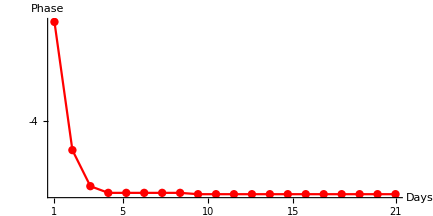

```mathematica
ListPlot[(tBm-tmo)[[2;;Dimensions[tBm-tmo][[1]]]],DataRange->{1,21},Joined->True,Mesh->All,PlotStyle->{PointSize[Large],Red},AxesStyle->Directive[Thick,FontSize->20],
BaseStyle->{FontFamily->"Helvetica",FontSize->20},AxesOrigin->{1,-9},Ticks->{{1,5,10,15,21},{0,-4,-8}},AxesLabel->{Days,Phase},PlotRange->{{1,22},{0,-9}},AspectRatio->0.5]
```